# Mathematica与数学建模 徐国栋

## 自我介绍

班级：自动化1402
姓名：徐国栋
毕业去向：浙江大学计算机学院
研究方向：人工智能，机器学习

数学建模经历
2016年华中赛   第一次参加数模比赛，三等奖
2016年国赛     湖北省二等奖
2017年美赛     国际一等奖（M）

比赛负责的部分：主要编程，辅助建模、写作

编程语言：Mathematica, Matlab, Lingo.

其他：PhotoShop

```mathematica
Why Mathematica
```

非常非常简单..即使你不懂编程

### 求不定积分

```mathematica
∫1/(1-x^3)ⅆx
```

ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1-x]+1/6 Log[1+x+x^2]

### 画图

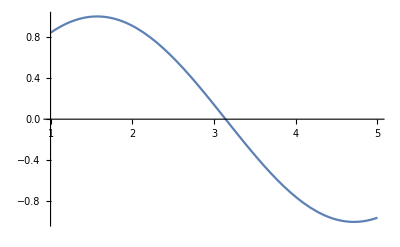

```mathematica
Plot[Sin[x],{x,1,5}]
```

### 自然语言

#### 如果我们想求出前500个质数的和, 又不想编程?

```mathematica
LinguisticAssistant
```

824693

```mathematica
GeoDistance[Entity["City",{"Shanghai","Shanghai","China"}], Entity["City",{"Beijing","Beijing","China"}]]
```

1068.58 km

```mathematica
我们想知道上海到北京的距离？
```

交互式的环境

```mathematica
Manipulate[Plot[am*func[w*x],{x,-5,5}],{w,1,5},{am,1,5},{func,{Sin,Cos,Tan,ArcTan,ArcSin}}]
```

```mathematica
一个例子: 摆线



即一个圆在平面上滚动时, 其上一个点形成的轨迹. 我们很难自己想象出这样一个轨迹的形状. 


 利用其交互性的功能, 我们很容易可以仿真出这条轨迹.
```

## 摆线

```mathematica
d=3;R=3;
Animate[ParametricPlot[{R t-d Sin[t],R-d Cos[t]},{t,-Pi,t},PlotStyle->{Thick,Blue}],{t,-Pi+0.01,4Pi}]
```

```mathematica
Animate[Show[ParametricPlot[{R t-d Sin[t],R-d Cos[t]},{t,-Pi,t},PlotStyle->{Thick,Blue}],Graphics[{{Circle[{R t,R},R]},{Thick,Line[{{R t,R},{R t-d Sin[t],R-d Cos[t]}}]},{Line[{{-R Pi,0},{3 R Pi,0}}]},{Red,Disk[{R t-d Sin[t],R-d Cos[t]},0.1*R]}}],PlotRange->{{-R Pi,3 R Pi},{-d,R+d}},Axes->None],{t,-Pi+0.01,3 Pi}]
```

函数式编程

### 运算基于函数, 有函数式编程的很多好处. 如函数重载，无副作用，高阶API。 想学函数编程的同学可以尝试看一下SICP, 学习一下Scheme语言, 进一步可以尝试Haskell语言. 这是一门纯函数式的语言, 一些特性非常奇妙, 比如惰性求值, 高阶函数等, 这里顺便提一句，我们知道编程主要有三大范式，面向对象，面向过程，函数式编程。其中函数式编程最大的优点就是纯函数的无副作用，所谓无副作用，就是说函数内部不会修改函数外的状态，所有的事情都发生在函数内部，函数是第一公民，所有的操作都围绕函数展开。这样做的优点是，在编写高并发的程序的时候，不用太多的考虑各个函数之间的状态干扰问题，从而可以很容易的编写并行化的程序。 -Graphics- -Graphics-

## 元胞自动机-Conway 生命游戏

```mathematica
在一个有边界的二维网格(Grid)中，每个格子中生活着一个细胞(Cell)；每个细胞只有两种生命状态：生(Alive)或死(Dead)；网格矩阵边界之外没有细胞；

每天天一亮，所有格子里的细胞都统一通过下面4个规则，进化到下一代。每个细胞下一代的生命状态与自己和8个邻居进化前的生命状态有关：

1）对于活的细胞，若其活着的邻居过于稀少，以至于少于2个，那么它的下一代就死去了；
2）对于活的细胞，若其活着的邻居过于稠密，以至于多于3个，那么它的下一代也会死去；
3）对于活的细胞，若其活着的邻居恰好是2~3个，那么它的下一代会接着愉快地活着；
4）对于死的细胞，若其活着的邻居恰好是3个，那么它的下一代会复生。
```

## 元胞自动机

```mathematica
函数重载
```

```mathematica
6行代码
```

```mathematica
check=RandomInteger[1,{100,100}];
updata[1,2]:=1;
updata[_,3]:=1;
updata[_,_]:=0;
SetAttributes[updata,Listable]
Dynamic[ArrayPlot[check=updata[check,Plus@@Map[RotateRight[check,#]&,{{-1,-1},{-1,0},{-1,1},{0,1},{0,-1},{1,-1},{1,0},{1,1}}]]]]
```

强大的内置函数

### 基于函数式编程, 内置函数非常多, 并且功能非常完善.

## 分形

Julia集-复数域


f(z)=z^2+c 对一个复平面上的任一点, 用这个函数对其进行迭代, 可以形成一个迭代序列, {f(z), f(f(z)), f(f(f(z))), f(f(f(f(z)))), ...}, 这个序列的模的收敛性根据点的位置不同是不同的.

## 分形

也就是说对f(z)=z^2+c, 任何一个不同的C, 我们都可以确定出一个不同的Julia集.

实现上, 首先我们定义一个迭代函数, 给定一个复平面上的点 z = x + y * i 对其进行Julia集的迭代, 输出为其模逃逸出2的迭代次数, 输入为X,Y,C_x, C_y, 以及迭代序列的长度(因为我们没办法计算到无穷大).

```mathematica
julia[x_,y_,lim_,cx_,cy_]:=
 Block[{z,ct=0},z=x+I*y;
    While[(Abs[z]<2.0)&&(ct<lim),++ct;
  z=z*z+(cx+I*cy);];Return[ct];]
```

```mathematica
DensityPlot[julia[x,y,50,0.11,0.66],
                {x,-1.5,1.5},{y,-1.5,1.5},
                  PlotPoints->120, Mesh->False]
```

-Graphics-

## 分形

```mathematica
内置函数, 性能有专门的优化, 并且一些参数会为你自动选择, 不需要调参数, 我们前面的参数就是序列长度. 利用内置函数, 我们只需要提供C的值.
```

```mathematica
JuliaSetPlot[0.11+0.66I,PlotLegends->Automatic]
```

-Graphics-

```mathematica
MandelbrotSetPlot[{-0.65+0.47I,-0.4+0.72I},MaxIterations->200,ColorFunction->"RedBlueTones"]
```

-Graphics-

适合任何人, 不仅仅是数学建模

### 不管你是什么专业, 它都有相应的功能.

## 数学

### 一个例子 - 积分

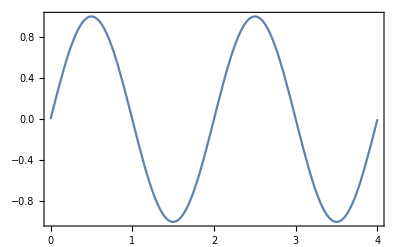

```mathematica
intEg1Plt1=Plot[Sin[π x],{x,0,4},AxesOrigin->{0,0},Frame->True]
```

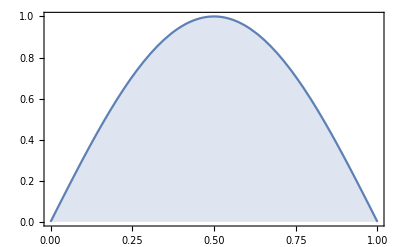

```mathematica
intEg1Plt2=Plot[Sin[π x],{x,0,1},AxesOrigin->{0,0},Filling->Axis,Frame->True]
```

```mathematica
LeftValue[f_,{x_,a_,b_}]:=N[f/.x->a];
MidpointValue[f_,{x_,a_,b_}]:=N[f/.x->(a+b)/2];
RightValue[f_,{x_,a_,b_}]:=N[f/.x->b];
Sample[f_,{x_,a_,b_},type_]:={LeftValue[f,{x,a,b}],MidpointValue[f,{x,a,b}],RightValue[f,{x,a,b}]}[[type]];
BlockCoords[a_,b_,h_]:={{a,0},{a,h},{b,h},{b,0}};
RiemannBlocks[f_,{x_,a_,b_,n_},type_]:=Plot[f,{x,a,b},Prolog->Table[({{GrayLevel[0.8],Polygon[#1]},Line[Append[#1,#1[[1]]]]}&)[(BlockCoords[#1,#2,Sample[f,{x,#1,#2},type]]&)[a+i*((b-a)/n),a+(i+1)*((b-a)/n)]],{i,0,n-1}],Frame->True]
```

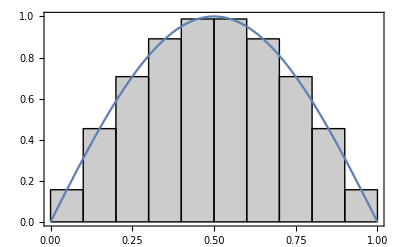

```mathematica
RiemannBlocks[Sin[π x],{x,0,1,10},2]
```

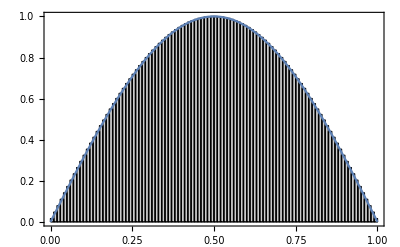

```mathematica
RiemannBlocks[Sin[π x],{x,0,1,100},2]
```

```mathematica
(∫_0)^1 f(x)dx
```

## 化学

```mathematica
毛地黄皂苷
```

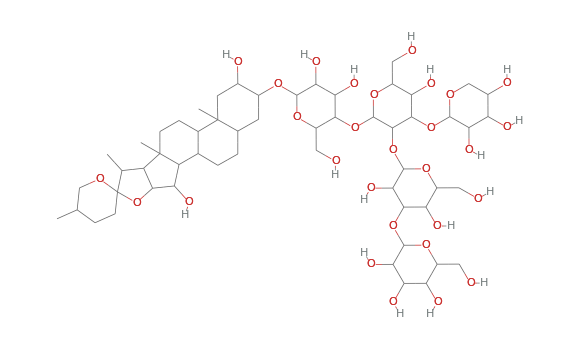

```mathematica
ChemicalData["Digitonin","ColorStructureDiagram"]
```

```mathematica
ChemicalData["Digitonin","MoleculePlot"]
```

```mathematica
g=Graph[ChemicalData["Digitonin","EdgeRules"],GraphLayout->"SpringEmbedding"]
```

## 数学建模中的应用

数据类型题目 - 拟合

数据类型题目 - 插值

数据类型题目 - 预测问题

微分方程

优化问题

图论

数据类型题目 - 拟合

#### 2011数学建模C问题一 : 对未来中国经济发展和工资增长的形式作出你认为简化、合理的假设, 并参考附件1, 预测从2011年至2035年的山东省职工的年平均工资.

### 数据分析流程

#### 导入数据 清理数据 分析数据

## 2011数学建模C

```mathematica
1. 导入数据
2. 清理数据
3. 分析数据
```

```mathematica
filepath = "/users/xuguodong/desktop/cumcm2011C附件1-山东省职工平均工资.xls";
```

```mathematica
rawData = Import[filepath,{"Data",1}]
```

```mathematica
data = Cases[rawData,{_Real,_Real}]
```

```mathematica
DateListPlot[data⟦All,2⟧,{{1978,1,1},Automatic ,"Year"},Joined->True,Filling->Axis]
```

## 经典模型 - 人口增长logistic模型

### 对于这样一个建立好的模型, 我们只需要丢进数据进行最小二乘拟合出需要的参数即可.

```mathematica
Clear[K,Subscript[N, 0],r,t];
fit = FindFit[data⟦All,2⟧,(K Subscript[N, 0])/(Subscript[N, 0]+(K-Subscript[N, 0]) ⅇ^(-r t)),{K,Subscript[N, 0],r},t]
```

```mathematica
model=(K Subscript[N, 0])/(Subscript[N, 0]+(K-Subscript[N, 0]) ⅇ^(-r t))/.fit
```

```mathematica
nonlm=NonlinearModelFit[data⟦All,2⟧,(K Subscript[N, 0])/(Subscript[N, 0]+(K-Subscript[N, 0]) ⅇ^(-r t)),{K,Subscript[N, 0],r},t]
```

```mathematica
nonlm["Properties"]//Short
```

```mathematica
nonlm["BestFitParameters"]
```

```mathematica
nonlm["FitResiduals"]
```

```mathematica
nonlm["ANOVATable"]
```

```mathematica
Plot[nonlm["BestFit"],{t,0,80},Epilog->{Red,PointSize[Medium],Point[{Range[Length[data]],data⟦All,2⟧}ᵀ]}]
```

数据类型题目 - 插值

### 直接使用Interpolation函数, 而在Matlab, 你需要根据数据为几维, 是否为网格数据, 选择去用interp1, interp2, griddata(V4), csapi(三次样条), spapi(B样条)等等一大堆......其接口也不是很一致.

```mathematica
data=Table[{X[[i]],Y[[j]],Z[[i,j]]},{i,6},{j,6}];
data=Flatten[data,1];
ListPointPlot3D[data,PlotStyle->Red]
```

```mathematica
f=Interpolation[data]
Show[Plot3D[f[x,y],{x,0,100},{y,0,200}],ListPointPlot3D[data,PlotStyle->Red]]
ContourPlot[f[x,y],{x,0,100},{y,0,200}]
```

数据类型题目 - 预测问题

"LinearRegreesion" | "线性回归"
"NearestNeighbors" | "最近邻方法"
"RandomForest" | "随机森林"
"NeuralNetwork" | "神经网络"

### 常用的预测算法在Mathematica内部都有集成, 我们直接调用Predict函数, 它会为你选出最适合的算法. 说下神经网络, 很多人喜欢用, 原因如下. 1. 理论很复杂，内容很多，可以在论文里贴很多介绍性的文字。 2. 不需要解释结果怎么来的, 因为你也不知道怎么来的。 一般来说, 不要把神经网络作为主要的算法, 因为可解释性太弱, 可以夹杂在你的模型里, 但是不要作为主体。 推荐作为主体的算法 1. 随机森林 2. xgboost （这是一个gradient boost实现，有python binding，大家可以试试，现在很多数据挖掘比赛用这个效果非常好，且不需要怎么调参数） 3. 支持向量机SVM

```mathematica
Predict
```

## 葡萄酒品质打分预测

### 这里直接调用Mathematica自带的葡萄酒数据集. 这个葡萄酒的数据集包含 3600 组训练集, 和 1200 多组的测试集合, 11 个属性是葡萄酒的11 种化学成分. 通过化学分析可以来推断葡萄酒的质量 (1 ~ 10).

```mathematica
trainingset=ExampleData[{"MachineLearning","WineQuality"},"TrainingData"];
```

```mathematica
trainingset⟦;;3⟧
```

```mathematica
ExampleData[{"MachineLearning","WineQuality"},"VariableDescriptions"]
```

```mathematica
{Histogram[trainingset[[All,1,11]], PlotLabel-> "alcohol"],Histogram[trainingset[[All,1,9]], PlotLabel-> "pH"]}
```

```mathematica
p=Predict[trainingset]
```

```mathematica
unknownwine = {7.6,0.48,0.31,9.4,0.046,6.,194.,0.99714,3.07,0.61,9.4};
p[unknownwine]
```

```mathematica
quality[pH_,alcohol_]:=p[{7.6,0.48,0.31,9.4,0.046,6.,194.,0.99714,pH,0.61,alcohol}];
```

```mathematica
Show[g3=Plot3D[quality[pH,alcohol],{pH,2.8,3.8},{alcohol,8,14},AxesLabel->Automatic],ListPointPlot3D[{{3.07,9.4,p[unknownwine]}},PlotStyle->{Red,PointSize[.05]}]]
```

## 微分方程

lorenz方程

## Lorenz方程

```mathematica
NDSolve[{x'[t]==-10 (x[t]-y[t]),y'[t]==-x[t] z[t]+28 x[t]-y[t],z'[t]==x[t] y[t]-8/3*z[t],x[0]==5,z[0]==17,y[0]==13},{x,y,z},{t,0,200},MaxSteps->Infinity];
```

```mathematica
Animate[ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.%],{t,0,umax},PlotPoints->10000,ColorFunction->(ColorData["Rainbow"][#4]&),Boxed->False,Axes->False],{umax,0.1,50},AnimationRate->1.2]
```

## 优化问题 函数 | 求解 | 算法 "FindMaximum, FindMinimum" | 数值局部最优化 | 线性规划方法、非线性内点算法、利用二阶导数 "NMaximize, NMinimize" | 数值全局最优化 | 线性规划方法、Nelder-Mead、差分进化、模拟退火、随机搜索 "Maximize, Minimize" | 精确全局最优化 | 线性规划方法、柱形代数分解、拉格朗日乘子法和其他分析方法、整数线性规划 "LinearProgramming" | 线性最优化 | 线性规划方法(单纯型法、修正单纯型法、内点法)

## 优化问题

绝⼤多数建模问题都可以转换成优化问题，一般其中的⽬标函数与约束条件都会很复杂。因此，很多优化问题并不存在显⽰解（解析解），而需要使⽤基于数值⽅法的优化算法找到近似解。这类优化算法⼀般通过不断迭代更新解的数值来找到近似解。我们讨论的优化都是这类基于数值⽅法的算法。

常见的数值优化方法主要分为两类。

一类是传统的方法，这类方法在机器学习，深度学习中应用非常广泛，因为其求解稳定，计算复杂度低，适应性与理论性都更强一些，其一般是针对结构化的问题，有较为明确的问题和条件描述，如线性规划，二次规划，整数规划，混合规划，带约束和不带约束条件等，即有清晰的结构信息。这类方法根据使用的梯度信息不同又可以分为三种，1. 无梯度方法，如单纯形法，2. 一阶梯度方法，如共轭梯度法，梯度下降法，伪牛顿法（伪牛顿法有很多变种，如常用的L-BFGS），3. 二阶梯度法（hessian 矩阵），如牛顿法。

二是智能算法，这类方法在数学建模中用的最多，因为建模中的优化问题普遍比较缺乏结构信息，一般都是非凸，多极值的，这时候我们需要利用智能算法在跳出局部最优和收敛之间进行平衡。具体的方法上，用的最多的有模拟退火，遗传算法，还有诸如粒子群，蚁群，蛙群，狼群各种各种的变种。虽然变种很多，但万变不离其宗，这类算法事实上都是随机算法，只是各个算法用的随机化策略不同，并且用了一些”智能”的方法来限制与更新随机搜索的范围。

具体到求解的时候, 最好能找到一个好的初始解给算法(自己从题目的理解提供一个好的初始解), 能很大程度的改善计算时间和计算结果.

下面举个例子看看传统算法在找极值点上的影响，以及起始点的重要性。

## 优化问题

```mathematica
Manipulate[
Module[{min,pts,init},
{min,pts}=Reap[
Quiet[
FindMinimum[f,{{x,r⟦1⟧},{y,r⟦2⟧}},Method->mm,StepMonitor:>If[Norm[{f,x,y}]<10000,Sow[{x,y,f+0.001}]]]
]
];

init=Append[r,f+0.001/.{x->r⟦1⟧,y->r⟦2⟧}];

Show[
Plot3D[f,{x,-7,7},{y,-7,7},
Mesh->30,
MeshFunctions->{#3&},
MeshStyle->GrayLevel[0.6],
PlotLabel->If[Length[pts]==0,Style["No minimum was found.","Label"],Row[{Style["初始点",Green,13,"Label",FontFamily->"微软雅黑"],Style["中间点 points",Darker[Yellow],13,"Label",FontFamily->"微软雅黑"],Style["极值点",Red,13,"Label",FontFamily->"微软雅黑"],Style[Row[{Length[pts⟦1⟧]," 迭代"}],"Label",13,FontFamily->"微软雅黑"]},Spacer[40]]],
PlotStyle->Opacity[.5],
PlotRangePadding->0,
Axes->None,
PlotTheme->"Frame"
],

Graphics3D[
If[Length[pts]==0,
{},
{
{PointSize[.02],Red,Point[Last[Last[pts]]],Green,Point[init],PointSize[.01],Darker[Yellow],Point[pts]},
Thickness[Medium],
Line[Insert[pts,init,{1,1}]]
}
]
],
ImageSize->500,Background-> White
]
],
Style["求函数最小值",15,FontFamily->"微软雅黑"],
Delimiter,"","",
{{r,{-2.5,5},"初始点位置"},{-5,-5},{5,5},ImageSize->Small},
Delimiter,"","",
{{f,(-1/(5+(x-2)^2+(y-2)^2)-1/(4+(x+3)^2+(y+3)^2)),"函数"},{x^2-y^2->"山谷型函数",(x^2/2-0.065625 x^4+x^6/384-(x y)/2+y^2)->"碗型函数",(-1/(5+(x-2)^2+(y-2)^2)-1/(4+(x+3)^2+(y+3)^2))->"双井函数"}
},
Delimiter,"","",
{{mm,Automatic,"最优化算法"},{Automatic->"自动选取","Gradient"->"Gradient","ConjugateGradient"->"Conjugate Gradient","PrincipalAxis"->"Principal Axis","LevenbergMarquardt"->"Levenberg Marquardt","Newton"->"Newton","QuasiNewton"->"Quasi Newton","InteriorPoint"->"Interior Point"}},
LabelStyle->14,ControlPlacement->Right,Paneled->False
]
```

## 优化问题

```mathematica
搜索 f(x,y)=ⅇ^(Sin(50 x))+1/4 (x^2+y^2)+Sin(60 ⅇ^y)-Sin(10 (x+y))+Sin(70 Sin x)+Sin(Sin(80 y)) 的全局极值
```

### 这个函数经常被用来测试一个优化算法的性能, 因为它的形状非常奇葩....我们看看它长什么样

```mathematica
Plot3D[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"RandomSearch"}]
```

{-2.38708,{x→-0.124868,y→0.290932}}

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"RandomSearch","SearchPoints"->1000}]
```

{-3.20814,{x→-0.394526,y→-0.0932002}}

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"SimulatedAnnealing","PerturbationScale"->9,"BoltzmannExponent"->Function[{i,df,f0},-df/(Exp[i/10])]}]
```

{-2.90519,{x→-0.394532,y→-0.721187}}

```mathematica
Show[Plot3D[{ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],First@%},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->{Opacity[0.6],Automatic},ImageSize-> 400],
Graphics3D[{Red,PointSize[Large] ,Point[-{0.0231,0.4942,3.14}]},ImageSize->250]]
```

## 图论

### 图论应该是属于对算法要求最高的一类, 但是我们一般很少碰到图论题, 当然如果你碰到了, 并且能做出来的话, 拿奖的几率很大. Mathematica在图可视化和图算法可用性方面可以说是最强的(当然这里不讨论符号运算).

最短路

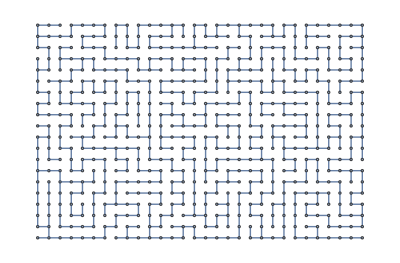

```mathematica
m=-Graphics-
```

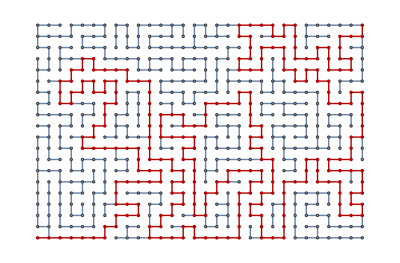

```mathematica
HighlightGraph[m,PathGraph[FindShortestPath[m,First@VertexList[m],Last@VertexList[m]]
]
]
```

最大流

```mathematica
g=-Graphics-
```

-Graphics-

```mathematica
ℱ=FindMaximumFlow[g,"Vancouver","Winnipeg","OptimumFlowData"];
ℱ["FlowValue"]
```

23

```mathematica
Grid[{#,ℱ[#]}&/@ℱ["EdgeList"],Frame-> All,Alignment-> Left]
```

```mathematica
Panel[Show[{CountryData["Canada","Shape"],ℱ["FlowGraph"]}, PlotRange->{{-0.31,0.083},{0.04,0.25}}]]
```

最小生成树

```mathematica
g = Graph[{1<->2,1<->4,2<->3,2<->5,3<->6,4<->5,4<->7,5<->6,5<->8,6<->9,7<->8,7<->10,8<->9,8<->11,9<->12,10<->11,11<->12,12<->13,10<->13,3<->5,8<->12},VertexSize->{0.8},EdgeStyle->{Directive[-Graphics-,Thickness[0.02]]}]
```

```mathematica
cablenetwork = FindSpanningTree[g];
HighlightGraph[g, cablenetwork, ImageSize -> 500]
```

TSP

### TSP应该是最常见的一类题目, 很多题目都可以转换成TSP问题进行求解, 在Matlab里我们一般用智能算法解. 而在Mathematica里我们只需要一行代码.

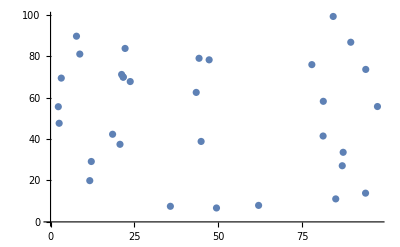

```mathematica
pts=RandomReal[100,{31,2}]/.{a_,b__}:> {a,b,a};
ListPlot[pts]
```

```mathematica
FindShortestTour[pts]
```

{449.188,{1,11,4,29,9,7,25,8,30,24,2,18,28,13,27,6,23,21,15,22,3,20,17,31,5,26,10,14,19,16,12,32,1}}

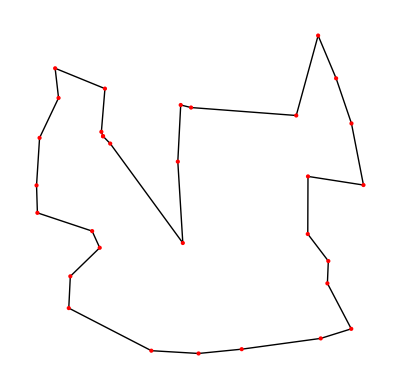

```mathematica
Graphics[{Line[pts⟦Last[FindShortestTour[pts]]⟧],PointSize[Large],Red,Point[pts]}]
```

## 一个好玩的例子 - 用TSP来画图

```mathematica
monalisa=-Graphics-;
```

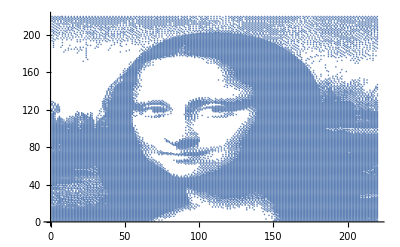

```mathematica
monalisa=ColorQuantize[ColorConvert[monalisa,"Grayscale"],2];
pos=PixelValuePositions[ImageAdjust[monalisa],0];
ListPlot[pos]
```

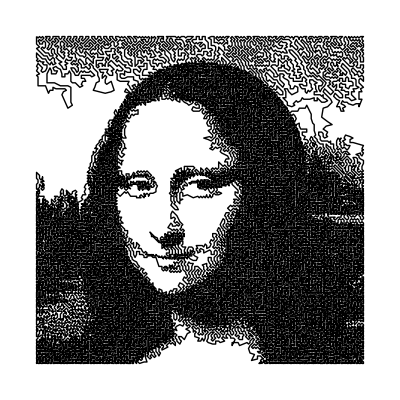

```mathematica
res=FindShortestTour[pos];
Graphics[Line[pos[[res[[2]]]]]]
```

## 资源

书籍
-Graphics-                               -Graphics-

帮助文档

官方的资源

```mathematica
demonstrations.wolfram.com 	
		Wolfram Library Archive 和 MathWorld™
```

```mathematica
这次讲的内容可以到下面的网站下载，包括pdf与源码。
https://github.com/memoiry/mathematica_road_to_modeling
```